### Capítulo 1 - Introdução à amostragem Seção 2 - Tamanho da amostra

Tamanho da população desconhecido (primeira aproximação):

n_0=1/E^2=E^-2.

E: Erro amostral tolerável (em porcentagem centesimal)

```mathematica
Clear[firstSampleSize]
firstSampleSize=Function[E,1/E^2];
```

```mathematica
Manipulate[Plot[firstSampleSize[EE],{EE,0,maxError},ImageSize->350,PlotLabel->"tamanho da amostra (1^a aprox.) em função \ndo erro, erro máx. variável",Frame->True,FrameLabel->{"Erro tolerável","Tam. amostra"}],{{maxError,0.05},0.001,1,0.01,Appearance->"Labeled"}]
```

Este não tem nenhuma referência fixa.

Tamanho da população conhecido:

n=(N·n_0)/(N+n_0).

N: tamanho da população
n_0: tamanho da amostra primeira aproximação

```mathematica
Clear[knownPopulationSizeSampleSize]
knownPopulationSizeSampleSize=Function[{N,maxError},(N*firstSampleSize[maxError])/(N+firstSampleSize[maxError])];
```

```mathematica
MapThread
```

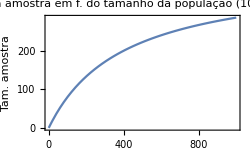
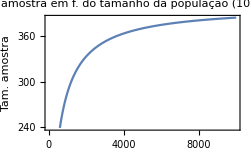

```mathematica
Table[Function[maxPopulationSize,Plot[knownPopulationSizeSampleSize[NN,0.05],{NN,0,maxPopulationSize},ImageSize->250,PlotRange->Automatic,Frame->True,FrameLabel->{"Tam. população","Tam. amostra"},PlotLabel->"tamanho da amostra em f. do tamanho \nda população ("<>ToString@maxPopulationSize<>"), erro fixo (50)"]]@@{mps},{mps,{1000,10000}}]
```

```mathematica
Manipulate[Plot[knownPopulationSizeSampleSize[NN,maxError],{NN,0,91230},
PlotLabel->"tamanho da amostra em f. do tamanho\n da população, erro variável",
ImageSize->250],{{maxError,0.05},0.01,1,0.01,Appearance->"Labeled"}]
```

Quanto mais erro tolerável, mais o teto do tamanho da amostra se aproxima ao da população; quanto menos, mais distantes estão.

Quanto mais erro tolerável, mais linearmente o tamanho da amostra cresce com o da  população; quanto menos, mais exponencialmente (aumenta rápido, mas para um número menor).

### Seção 3 - Distribuição amostral

A distribuição qui-quadrado é uma distribuição que tende à normal conforme os graus de liberdade aumentam.

Um teste qui-quadrado (“goodness of fit”) checa diferença entre valor observado e esperado.

A estatística variância tem distribuição amostral qui-quadrado.

```mathematica
Clear[data1];
data1=RandomVariate[NormalDistribution[10,5],100]
```

{4.66767,15.9696,9.52956,12.0938,18.3508,-0.963417,6.5015,13.45,10.0915,12.0857,5.96084,2.6883,10.2078,14.666,13.5376,-0.54474,14.0167,5.54866,5.10312,9.82946,7.70351,6.88086,12.3393,13.3115,13.2194,9.02091,8.11629,14.1728,12.3337,5.87177,14.9765,8.80841,8.32577,9.9964,-5.2463,14.6499,17.2626,6.94374,12.4604,13.2404,14.9162,13.6061,13.8394,15.6216,12.7151,11.792,6.43045,14.2761,7.91399,5.01538,9.66756,3.92264,5.15633,9.94272,13.6966,19.2929,11.6185,17.7924,14.8747,10.9683,14.3645,6.42013,16.8599,12.0642,9.87813,15.0767,10.6776,5.04709,18.5912,10.7515,13.8109,11.7377,7.57463,7.6314,11.8374,3.07636,4.34489,9.4501,15.7612,12.1626,4.52839,10.1979,9.77094,11.0678,15.1249,12.8252,10.2845,3.34165,8.54287,4.71463,9.0364,13.0014,19.0837,6.35384,6.70852,4.99074,0.753843,-5.24711,9.14218,5.02235}

```mathematica
RandomSample[data1,5]
```

{10.1979,4.99074,11.6185,8.32577,12.3337}

Isso quer dizer os valores da estatística da variância entre as amostras.
Tomar 100 amostras randômicas e descobrir a distribuição dos valores de variância das amostras.

```mathematica
Clear[VarDistr]
VarDistr=Function[{data,varf,sampleCount},Module[{samples,vars},
	Table[
		samples=Table[RandomSample[data1,5],{sampleCount}];
		vars=varf/@samples;
		Histogram[vars,12,ImageSize->Tiny]
	,15]
]];
```

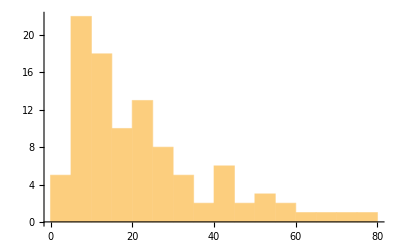
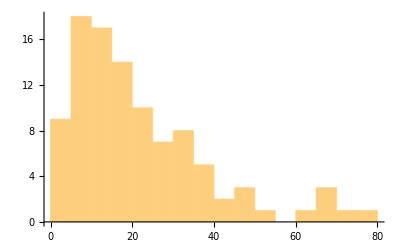
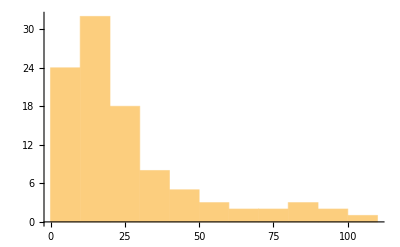
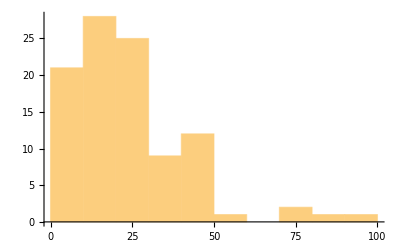
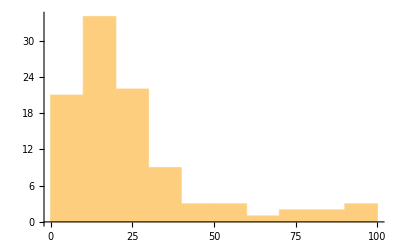
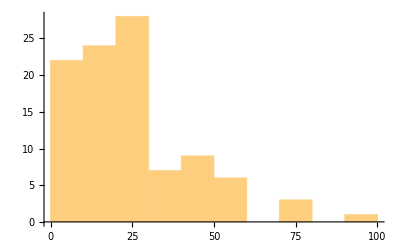
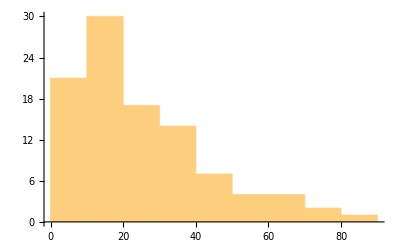
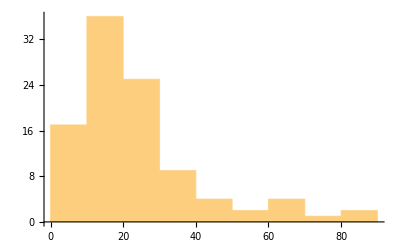

```mathematica
VarDistr[data1,Variance,100]
```

Fiz isso 15 vezes.

Sendo que a variância da população é

```mathematica
Variance[data1]
```

24.2114

E outra população?

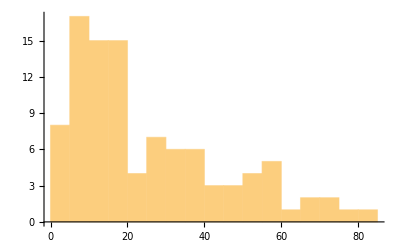
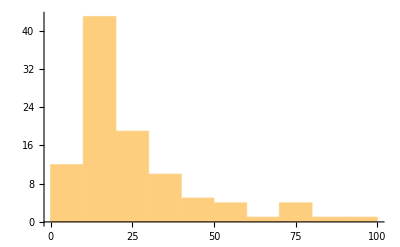
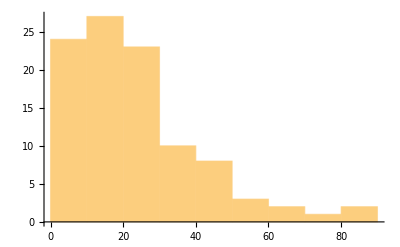
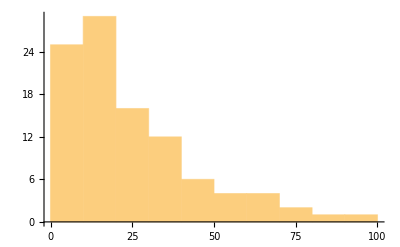
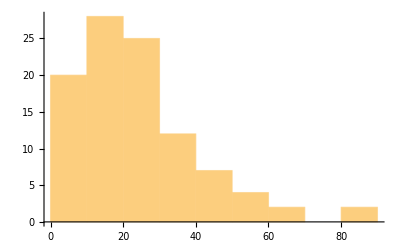
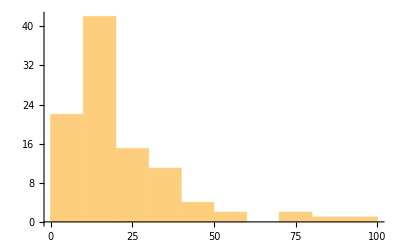
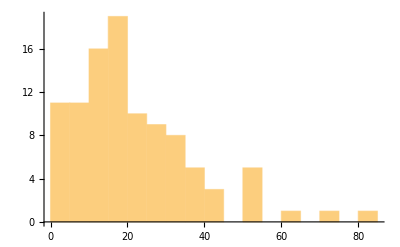
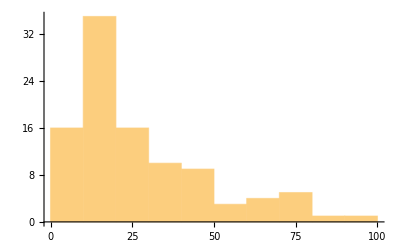

```mathematica
Clear[data2];
data2=RandomVariate[NormalDistribution[30,5],100];
VarDistr[data2,Variance,100]
```

```mathematica
Variance[data2]
```

24.1759

Mudei a média da população, mas a variância continuou a mesma... Mudar a variância.

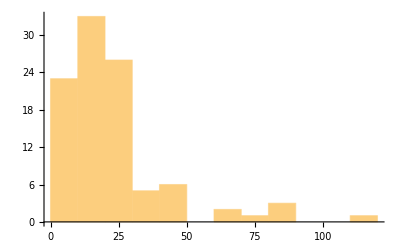
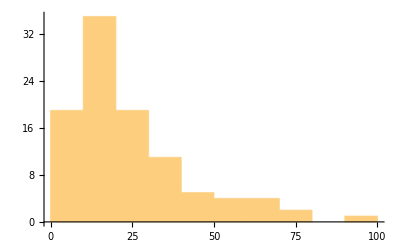
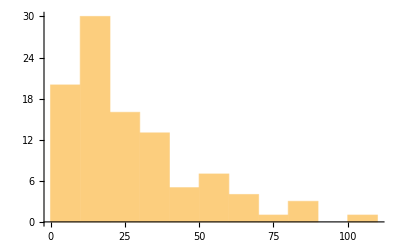
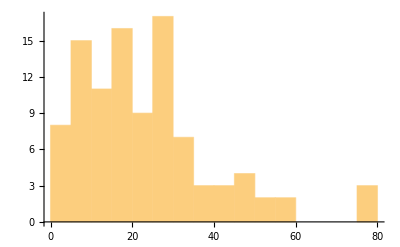
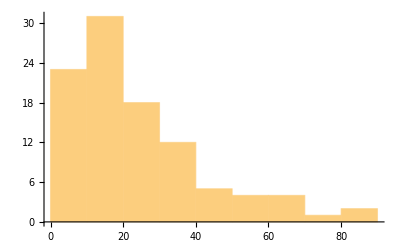
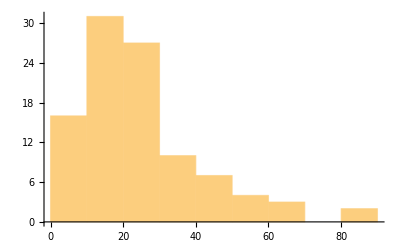
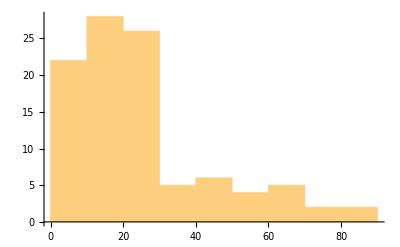
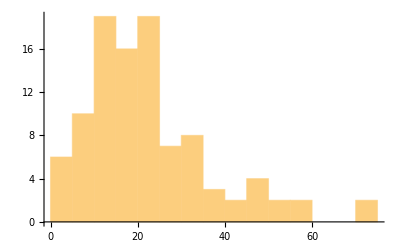

```mathematica
Clear[data2b];
data2b=RandomVariate[NormalDistribution[40,15],100];
VarDistr[data2b,Variance,100]
```

As frequências continuaram as mesmas, a distribuição a mesma... Só mudou o valor das variâncias.

O mesmo para a estatística “média”.

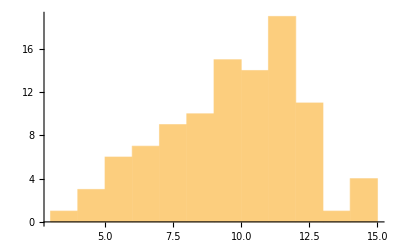
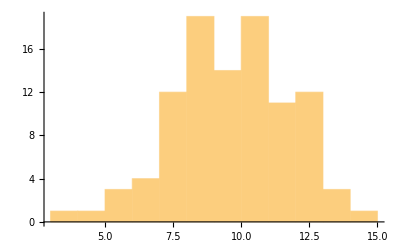
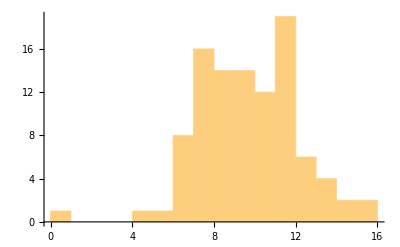
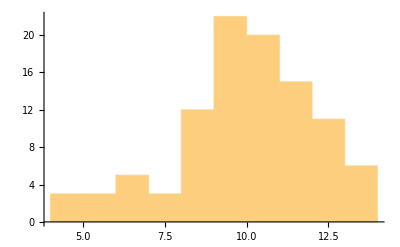
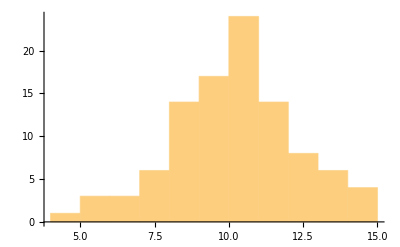
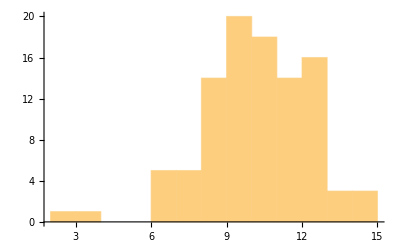
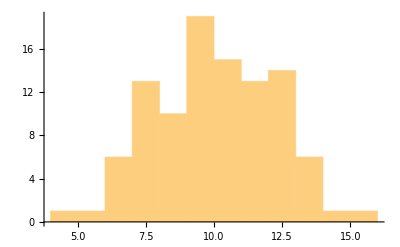
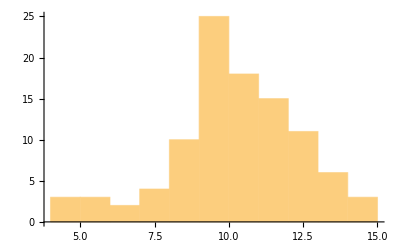

```mathematica
VarDistr[data1,Mean,100]
```

A média é normal.
Mas (p. 29) não igualmente normal à população. Demonstrar:

"Se a distribuição da população for normal, a distribuição amostral
de x̄ será também normal para quaisquer tamanho da amostra, pois será uma
combinação linear de variáveis independentes."

“Se a distribuição da população não for normal, mas a amostra for
suficientemente grande, resultará pelo teorema do limite central, que, no caso de
uma população infinita ou amostragem com reposição, a distribuição amostral de x̄ 
será aproximadamente normal, pois o valor de resultará da soma de um número
grande de variáveis aleatórias independentes.”

“A variância com que resultam dispersos os possíveis valores
da estatística x̄ é a enésima parte da variância da população origem da amostra.” (Imagem abaixo.)

Conceito de variáveis randômicas dependentes ou independentes.

Mesma distribuição (exata) significa mesma média e variância.

Primeiro, a média, quanto mais amostras, deverá tender mais à normalidade.

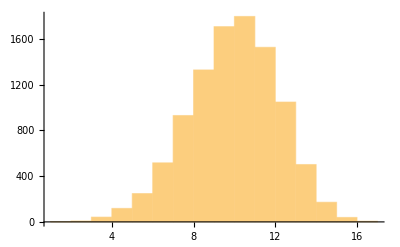
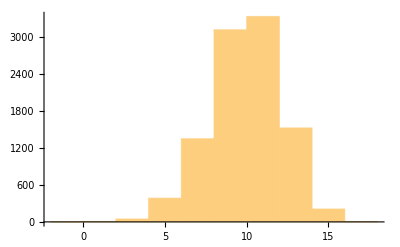
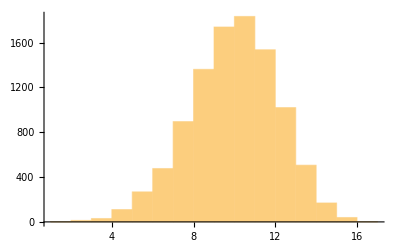
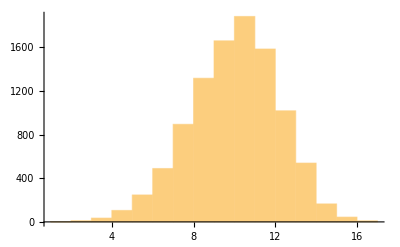
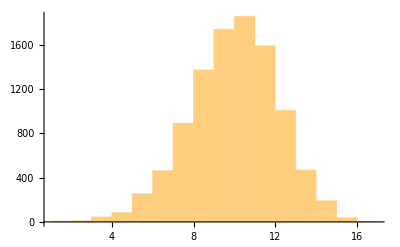
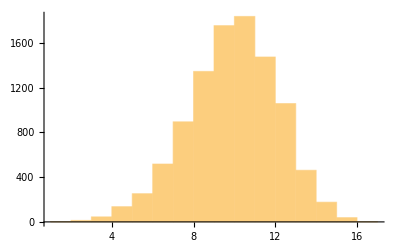
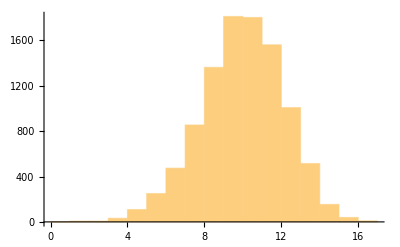
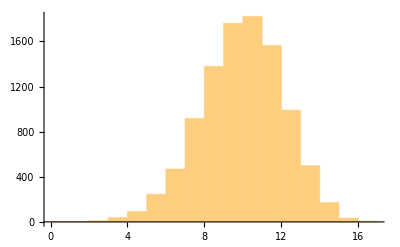

```mathematica
VarDistr[data1,Mean,10000]
```

E a variância?

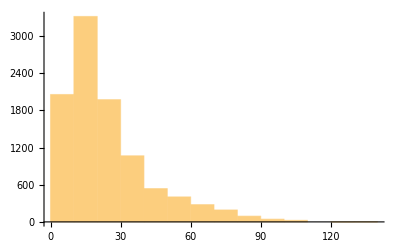
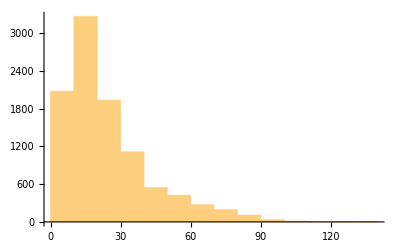
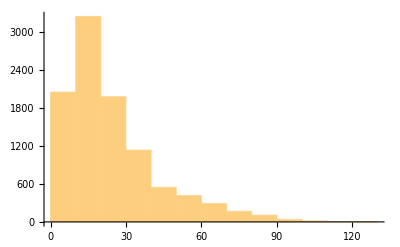
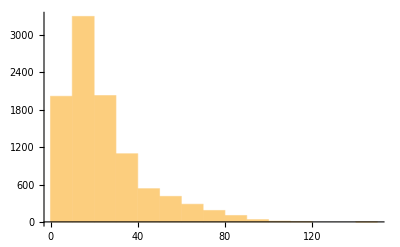
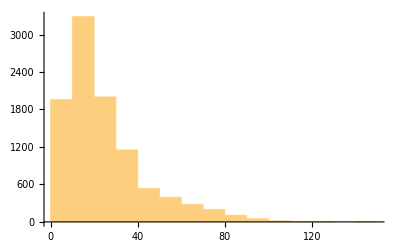
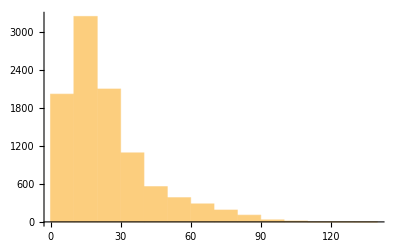
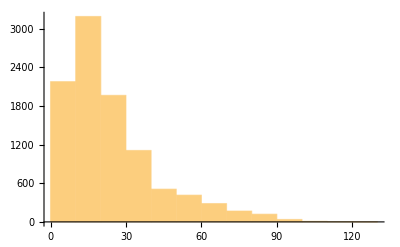
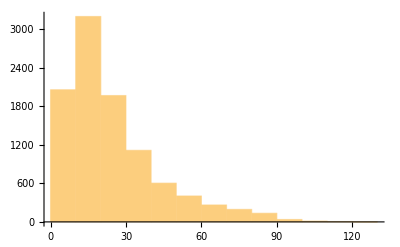

```mathematica
VarDistr[data1,Variance,10000]
```

Mais qui-quadrada.

Até agora, só as distribuições das estatísticas, ou seja, o valor em cada amostra separado.
Agora, estatísticas das estatísticas: um número único.
Primeiro, o item do gráfico, variância das médias.

O gráfico se refere a duas distribuições normais em que a média é a mesma e só a variância muda. Para ilustrar que a variância das médias das amostras é uma fração da variância (apenas variância) da população. Por isso, no sentido oposto, a variância da população pode ser estimada pela variância das médias das amostras.

### Chi-square

Chi-square (χ^2) é uma distribuição que é uma soma de n, ou melhor k, variáveis randômicas normais independentes (aos quadrados). Essa soma se distribui como qui-quadrado, e quanto maior k, ou mais variáveis randômicas, mais a distribuição tende à normal. k é também chamado de graus de liberdade da distribuição qui-quadrado, e é um parâmetro (no sentido de input) (o único) da distribuição.
Ou seja, ∑_(i=1)^k Z_i^2, em que Z_i é uma variável randômica.

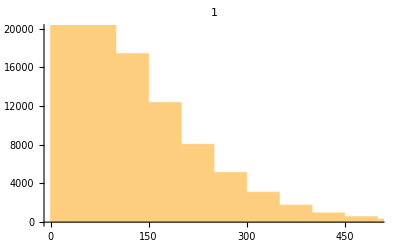
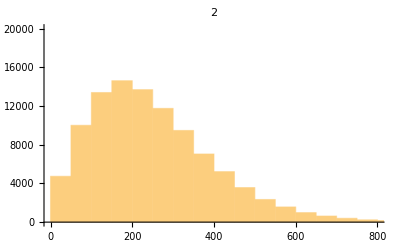
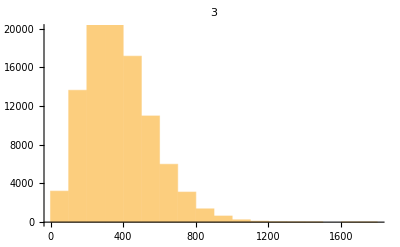
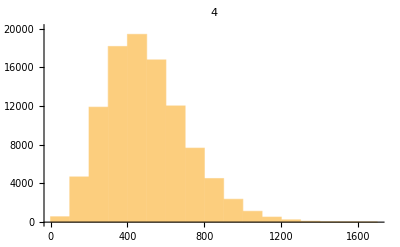
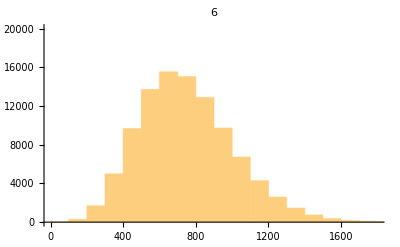
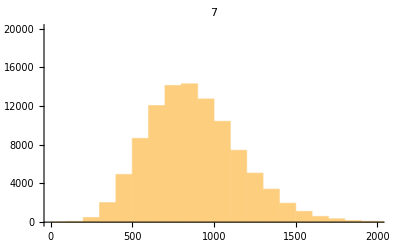
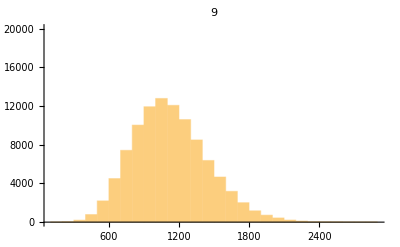
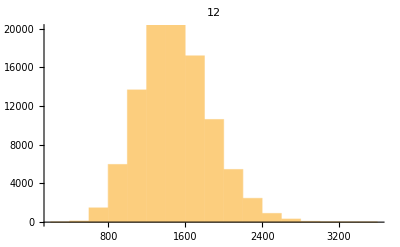

```mathematica
Module[{chi},
Table[
chi=∑_(i=1)^k RandomVariate[NormalDistribution[10,5],100000]^2;
Histogram[chi,20,ImageSize->Tiny,PlotLabel->k,PlotRange->{0,20000}]
,{k,{1,2,3,4,6,7,9,12}}]
]
```

Ou seja, k é quantas amostras são tiradas. (É tamanho da amostra, ver mais abaixo.)

```mathematica
RandomVariate[NormalDistribution[10,5],10]
```

{9.68438,11.1093,8.81397,12.203,14.8844,4.36354,3.04475,-5.72113,1.49031,12.5631}

```mathematica
RandomVariate[NormalDistribution[10,5],10]^2
```

{33.6406,292.27,4.27711,14.2377,198.639,106.311,0.757173,28.6468,128.299,318.371}

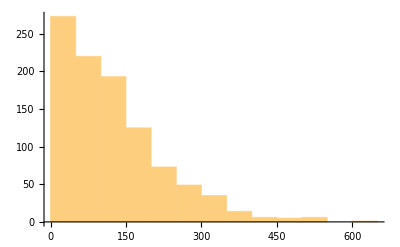
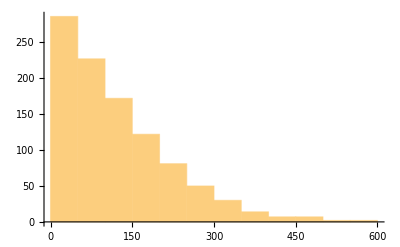
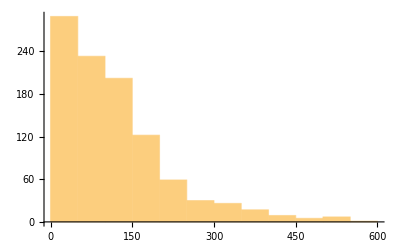
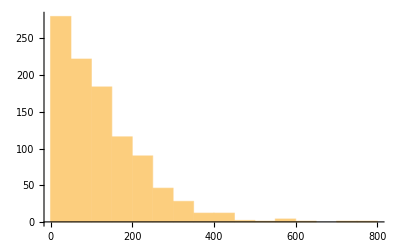
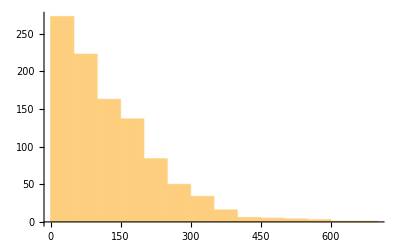
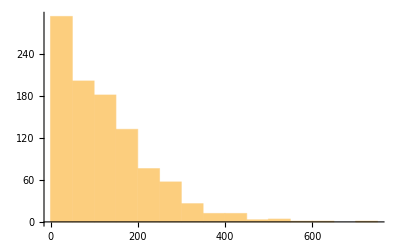
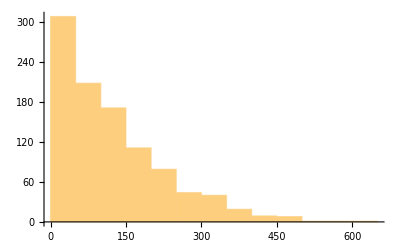
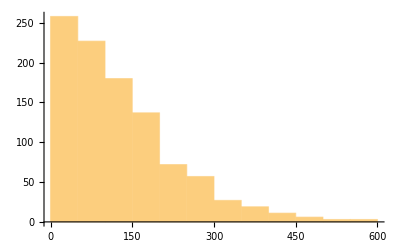

```mathematica
Module[{rv},
Table[
rv=RandomVariate[NormalDistribution[10,5],1000]^2;
Histogram[rv,15,ImageSize->Tiny]
,8]
]
```

Uma variável randômica tem esta distribuição (porquê?). n somadas ao quadrado tendem à normal. (Porquê?) Observa-se que 1 ou n somadas não ao quadrado não têm esta distribuição, são todas normais:

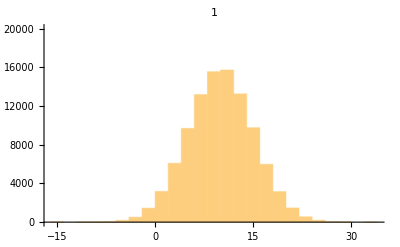
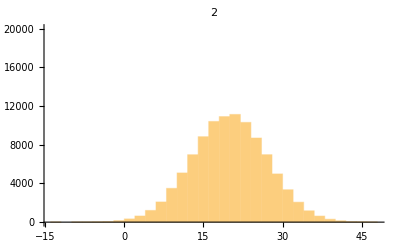
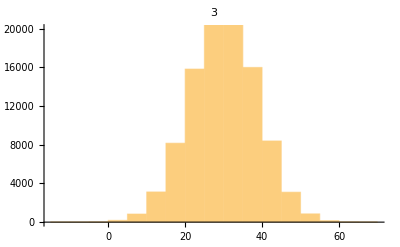
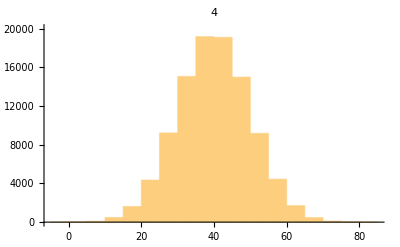
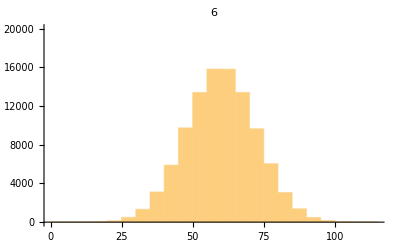
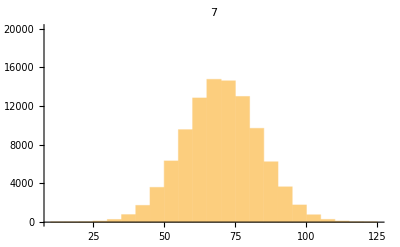
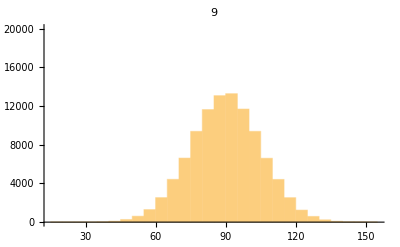
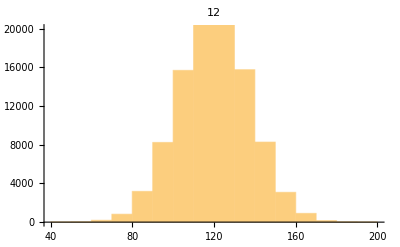

```mathematica
Module[{chi},
Table[
chi=∑_(i=1)^k RandomVariate[NormalDistribution[10,5],100000];
Histogram[chi,20,ImageSize->Tiny,PlotLabel->k,PlotRange->{0,20000}]
,{k,{1,2,3,4,6,7,9,12}}]
]
```

Este é apenas o comportamento normal da variável randômica normal.
A normal ao quadrado, dependendo da presença de negativos, os positiva, e por isso.
Então este deveria ser sempre normal.

Kendall (1937)1:

We have already seen that the sum of n normally distributed variates is itself normally distributed. The sum of the squares of n normal variates is not so distributed, however. In fact, the sum of the squares of n normal variates, drawn from a universe with unit standard deviation, is distributed in a form given by the equation y=y_0 ⅇ^(-∑^2/2)∑^(n-1) where ∑^2  is the sum in question.

Now it has already been shown that under the conditions assumed the xs are each distributed normally about zero mean, and it may be shown further that χ^2 may be regarded as the sum of the squares of v variates each distributed normally with unit standard deviation and about a zero mean. Hence the distribution of χ^2 is given by y=y_0 ⅇ^(-χ^2/2)χ^(v-1).

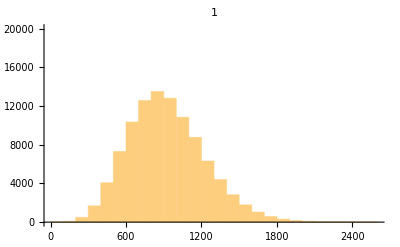
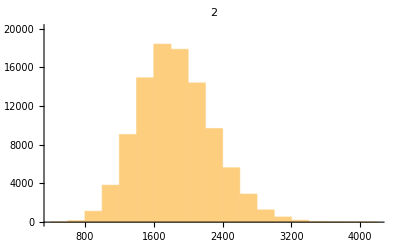
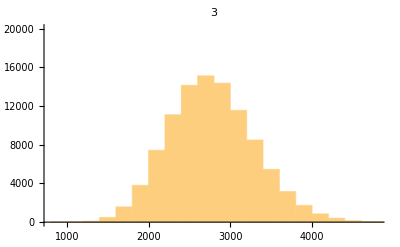
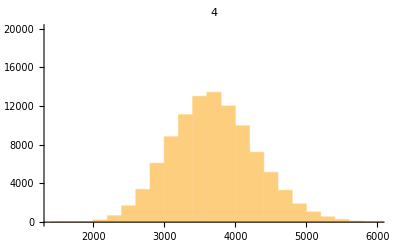
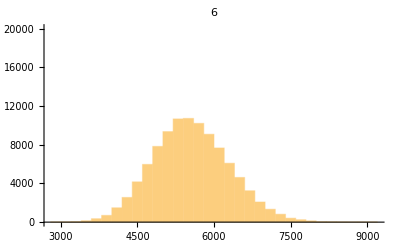
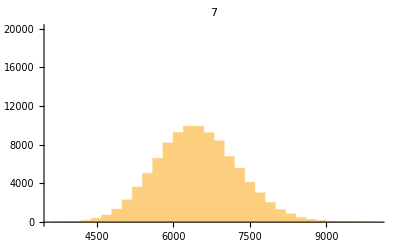
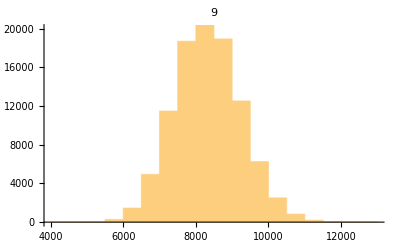
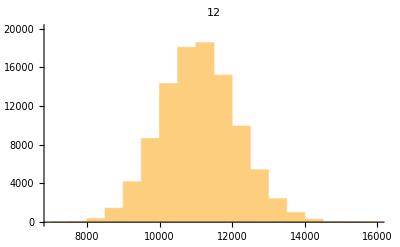

```mathematica
Module[{chi},
Table[
chi=∑_(i=1)^k RandomVariate[NormalDistribution[30,5],100000]^2;
Histogram[chi,20,ImageSize->Tiny,PlotLabel->k,PlotRange->{0,20000}]
,{k,{1,2,3,4,6,7,9,12}}]
]
```

“Test statistics that follow a chi-squared distribution arise from an assumption of independent normally distributed data, which is valid in many cases due to the central limit theorem. A chi-squared test can be used to attempt rejection of the null hypothesis that the data are independent.”2

Ou seja, a semelhança com uma distribuição chi-squared indicar se os dados são independentes.

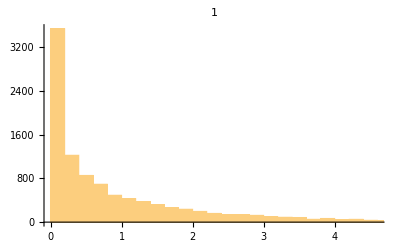
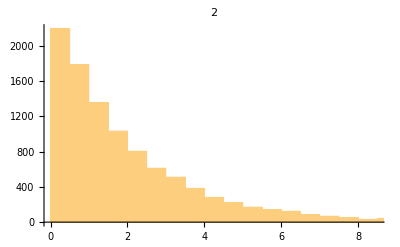
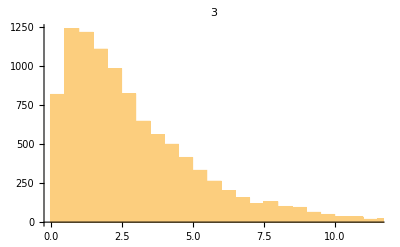
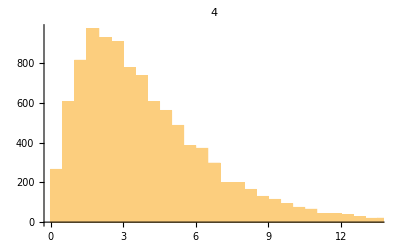
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[RandomVariate[ChiSquareDistribution[k],10000],PlotLabel->k],{k,1,8}]
```

```mathematica
{PDF[NormalDistribution[10,5]],PDF[NormalDistribution[20,10]]}
```

{Function[x,(ⅇ^(-1/50 (-10+x)^2))/(5 √(2 π))],Function[x,(ⅇ^(-1/200 (-20+x)^2))/(10 √(2 π))]}

```mathematica
Table[PDF[ChiSquareDistribution[k]],{k,1,2}]
```

{Function[x,Piecewise[{{ⅇ^(-x/2)/(√x √(2 π)), x>0}, {0, True}}],Listable],Function[x,Piecewise[{{ⅇ^(-x/2)/2, x>0}, {0, True}}],Listable]}

A estatística chi-square é:3

χ^2=((n-1)·s^2)/σ^2, onde 
n é o tamanho da amostra, 
σ é o desvio padrão da população, 
s é o desvio padrão da amostra.

A distribuição desta estatística entre as amostras é chi-square.

```mathematica
Clear[chiSqStat]
chiSqStat=Function[{pmean,psd,sampleSize,sampleCount,plotSize},Module[{chiSqs,sample,chiSq},
	chiSqs=Table[
		sample=RandomVariate[NormalDistribution[pmean,psd],sampleSize];
		(*Print[sample];*)
		chiSq=((sampleSize-1)*StandardDeviation[sample]^2)/psd^2;
		(*Print[chiSq];*)
		chiSq
	,sampleCount];
	Histogram[chiSqs,20,ImageSize->plotSize,PlotLabel->"size "<>ToString[sampleSize]<>
		" count "<>ToString[sampleCount]]
]];
```

```mathematica
Table[chiSqStat[0,5,sampleSize,sampleCount,Small],{sampleSize,{10,100,1000}},{sampleCount,{100,1000,10000}}]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Manipulate[Module[{},
chiSqStat[pmean,psd,sampleSize,sampleCount,{250}]
],{{pmean,0},-20,20,1},{{psd,5},0,20,.1},{{sampleSize,10},1,1000,1},{{sampleCount,2000},1,10000,1}]
```

Onde sampleCount é k são os graus de liberdade.
Analisando a fórmula da estatística, ela é (tamanho da amostra × variância da amostra)/(variância da população).

Refinetti, p. 83: “To avoid human subjectivity in determining what is and is not a flat wave, a mathematical index (usually a quotient of variances) is used”.

“The Chi Square distribution is very important because many test statistics are approximately distributed as Chi Square. Two of the more common tests using the Chi Square distribution are tests of deviations of differences between theoretically expected and observed frequencies (one-way tables) and the relationship between categorical variables (contingency tables).”4

“A standard normal deviate is a random sample from the standard normal distribution. The Chi Square distribution is the distribution of the sum of squared standard normal deviates. The degrees of freedom of the distribution is equal to the number of standard normal deviates being summed. Therefore, Chi Square with one degree of freedom, written as χ2(1), is simply the distribution of a single normal deviate squared.”5

Ou seja, a distribuição chi-square é a distribuição da soma das amostras ao quadrado. Os graus de liberdade são a quantidade de amostras. Portanto, com um grau de liberdade, o chi square é a distribuição de uma amostra ao quadrado.

A dúvida é, o que é a soma de variáveis randômicas. É somar cada elemento de cada amostra constituindo uma amostra soma de mesmo tamanho, ou somar todos os elementos de todas as amostras.

```mathematica
Clear[chiTry1]
chiTry1=Function[{sampleSize,sampleCount,plotSize,dbg},Module[{samples,sqs,sumSqs},
	samples=Table[RandomVariate[NormalDistribution[0,1],sampleSize],sampleCount];
	If[dbg,Print[samples]];
	sqs=samples^2;
	If[dbg,Print[sqs]];
	(*Soma em colunas (verificado)*)
	sumSqs=Sum[sqs[[i]],{i,Length[sqs]}];
	If[dbg,Print[sumSqs]];
	If[!dbg,Histogram[sumSqs,ImageSize->plotSize]]
]];
```

```mathematica
chiTry1[8,6,Tiny,True]
```

{{0.167072,2.19346,0.794639,-0.672058,0.00378342,1.38066,0.306486,2.13256},{1.61561,-2.0913,-0.400649,-0.577983,-1.35913,-0.776389,-1.35386,0.841499},{-0.760407,0.535702,-0.148466,0.0657285,0.10313,-0.997283,0.666866,-1.16103},{0.302845,-0.763628,2.12641,-0.526461,0.59755,-1.19499,-0.120641,-0.938795},{0.370309,-0.0558507,-0.922862,0.600177,0.895559,1.17534,-0.779884,1.38602},{-0.423278,-0.0753462,0.210883,-1.9165,-0.731077,0.420164,0.199478,-0.881675}}

{{0.0279131,4.81128,0.631451,0.451662,0.0000143142,1.90623,0.0939335,4.5478},{2.61018,4.37354,0.16052,0.334065,1.84722,0.602779,1.83293,0.70812},{0.578218,0.286977,0.0220421,0.00432024,0.0106357,0.994574,0.44471,1.348},{0.0917154,0.583127,4.5216,0.277161,0.357066,1.42799,0.0145542,0.881336},{0.137129,0.0031193,0.851674,0.360213,0.802025,1.38143,0.608219,1.92106},{0.179164,0.00567705,0.0444715,3.67299,0.534474,0.176538,0.0397915,0.777352}}

{3.62432,10.0637,6.23176,5.10041,3.55144,6.48954,3.03414,10.1837}

```mathematica
Manipulate[Module[{},
chiTry1[sampleSize,sampleCount,250,False]
],{{sampleSize,1000},1,1000,1},{{sampleCount,8},1,1000,1}]
```

A questão é que a normalidade vem muito rápido com os graus de liberdade (10, etc.). A distribuição só não é normal para muitos poucos graus de liberdade (<10).

A dúvida mais fundamental é se uma amostra é uma variável randômica, ou várias variáveis randômicas.

“In mathematical terms, given a probability distribution F, a random sample of length n is a set of realizations of n independent, identically distributed random variables with distribution F. (...) A sample concretely represents the results of n experiments in which the same quantity is measured.  Each measurement is drawn from the probability distribution F characterizing the population, so each measured height x_i is the realization of a random variable X_i with distribution F.”6

“Two random variables with the same probability distribution can still differ in terms of their associations with, or independence from, other random variables. The realizations of a random variable, that is, the results of randomly choosing values according to the variable’s probability distribution function, are called random variates.”7

“The distinction between random variable and random variate is subtle and is not always made in the literature. It is useful when one wants to distinguish between a random variable itself with an associated probability distribution on the one hand, and random draws from that probability distribution on the other, in particular when those draws are ultimately derived by floating-point arithmetic from a pseudo-random sequence.”8 (Porra!)

Então, supondo que acima nos mathematical terms se cita n random variables mas se significa n random variates. Ou seja, o random sample pode ser n realizações de n variáveis randômicas de mesma distribuição, OU n realizações de n random variates de uma variável randômica.

(É sensível porque, dependendo disso, a amostra é ou não uma ou mais variáveis randômicas.) Então, a amostra nem é nem não é nenhuma quantidade particular de variáveis randômicas. Mas é, certamente, uma coleção de variates randômicas (seja da mesma variável ou não).

Disso, para a soma. Cada elemento de uma amostra é um variate, então a soma de variates ou variables é soma dos elementos.

```mathematica
Clear[chiTry2]
chiTry2=Function[{sampleSize,sampleCount,plotSize,dbg},Module[{samples,sqs,sumSqs},
	samples=Table[RandomVariate[NormalDistribution[0,1],sampleSize],sampleCount];
	If[dbg,Print[samples]];
	sqs=samples^2;
	If[dbg,Print[sqs]];
	sumSqs=Table[Sum[sq[[i]],{i,Length[sq]}],{sq,sqs}];
	If[dbg,Print[sumSqs]];
	If[!dbg,Histogram[sumSqs,ImageSize->plotSize]]
]];
```

```mathematica
chiTry2[8,5,Tiny,True]
```

{{-1.24639,2.01202,-0.0318449,0.140773,0.275498,-0.311212,-0.395751,-0.720348},{-1.93621,-0.0685909,0.479871,0.996278,0.291186,0.739419,-0.84916,-1.70546},{-0.860647,-0.599738,-0.358254,1.64244,-0.127261,-0.0773095,-0.0966515,-1.45047},{-1.05778,1.19991,0.400814,0.590139,-0.00644402,-0.745037,-1.58901,0.533469},{-0.749692,-0.983738,-1.073,-0.666152,-0.179373,0.502877,0.127116,0.962131}}

{{1.5535,4.04821,0.0010141,0.019817,0.0758993,0.0968532,0.156619,0.518901},{3.7489,0.00470471,0.230276,0.99257,0.0847893,0.54674,0.721073,2.90861},{0.740713,0.359686,0.128346,2.69762,0.0161953,0.00597675,0.0093415,2.10385},{1.11889,1.43977,0.160652,0.348265,0.0000415254,0.55508,2.52495,0.284589},{0.562038,0.967741,1.15133,0.443758,0.0321745,0.252885,0.0161585,0.925697}}

{6.47081,9.23766,6.06173,6.43224,4.35178}

```mathematica
1.5534990238389947+4.048206800388882+0.0010140998776991407+0.01981696708244098+0.07589933821166088+0.09685317308178297+0.1566189034487372+0.5189008611007893
```

6.47081

```mathematica
Manipulate[Module[{},
chiTry2[sampleSize,sampleCount,250,False]
],{{sampleSize,6},1,1000,1},{{sampleCount,10000},1,10000,1}]
```

Agora k faz sentido como quantidade de variates randômicos, o que é o tamanho da amostra.

A quantidade de amostras (e mean e variance) não mudam nada na forma da distribuição, neste sentido.

Agora, (e não sei de onde a equação da referência 9 veio), interpretando a equação de que a estatística Chi Square é a soma dos quadrados dos elementos da amostra, ou χ^2=∑_(i=1)^k x_i^2 (em que k é o número de elementos da amostra porque o número de graus de liberdade na estatística Chi Square é igual ao número de elementos/observações), vemos que pode ter proporcionalidade com a variância pois apenas não é subtraído da média. (?)

Similaridades com outras estatísticas: várias.

x̄=(∑x)/N, 
S^2=(∑(x_i-x̄)^2)/(N-1), 
χ^2=∑x_i^2, apenas isso.

O k entra na definição da Chi Square apenas porque é de interesse, mas a somatória a k é implícita em todas estas três estatísticas.

A dúvida fica porquê χ^2 para k≤10 seria útil, como distribuição, sendo o tamanho da amostra necessário tão baixo.

Kendall (1937)10: Properties of the χ^2 distribution.

The curves y=y_0 ⅇ^(-x^2/2)χ^(v-1) and the probability function P derived from them have several interesting properties which are worth noticing. As χ^2 is essentially positive, we consider only positive values of the variate.

In the first place, it will be seen that when v=1 the curve is the normal curve with unit standard deviation, for positive values of the variate. Thus the test for v=1 may be reduced to testing the significance of deviations of a normally distributed variate.

When v>1 the curve is of the single-humped type. It is tangential to the x-axis at the origin (χ^2=0), rises to a maximum where χ^2=v-1 and then falls more slowly to zero as χ^2 increases indefinitely. It is thus skew to the right.

As v increases, the curve becomes more and more symmetrical. In fact, when v is large, √(2 χ^2) is distributed approximately normally about a mean √(2v-1) with unit standard deviation. This result, due to R. A. Fisher, enabled us to dispense with tables of P for large values of v, say v>30, and to use the probability integral instead. In practice large values of v are rather infrequent.

O mean (pico) da chi-square é em k-1.

### Poisson

Eventos no tempo.

```mathematica
Table[ListLinePlot[RandomVariate[PoissonDistribution[mean],100],ImageSize->Small],{mean,{10,100,1000}}]
```

{-Graphics-,-Graphics-,-Graphics-}

Dispersões...

```mathematica
Module[{values},
Table[
values=RandomVariate[PoissonDistribution[mean],100000];
Print["mean ",mean,": std dev ",N@StandardDeviation[values]];
,{mean,{10,100,1000}}]
];
```

mean 10: std dev 3.1569

mean 100: std dev 10.0345

mean 1000: std dev 31.5798

```mathematica
Manipulate[Module[{},Histogram[RandomVariate[PoissonDistribution[mean],10000],ImageSize->250,PlotRange->{0,2500}]],{{mean,500},1,1000,1}]
```

```mathematica
Manipulate[Module[{},DiscretePlot[PDF[PoissonDistribution[mean],x],{x,-5,30},ImageSize->250,PlotRange->{0,0.2},PlotMarkers->Automatic]],{{mean,10},.01,20,.01}]
```

```mathematica
Manipulate[Module[{},Plot[PDF[NormalDistribution[mean,var],x],{x,-5,30},ImageSize->250,PlotRange->{0,0.2}]],{{mean,10},0.1,20,.1},{{var,3},2.1,6,.1}]
```

Poisson é discreto, e não-negativo; normal é contínuo e negativo ou positivo.
Outros fatores que diferenciam as distribuições são os formatos exatos dos picos e das caudas.

### Capítulo 2 - Estimação de parâmetros Seção 1 - Estimador e estimativa

Cada estatística fornece um dado sobre a população. Mas (presumivelmente a partir da forma como são calculadas) podem ter comportamentos classificáveis com respeito aos parâmetros.

A média da estatística (entre amostras) ser o próprio valor do parâmetro. (“Justo”, “não-enviesado”.)

A dispersão (variância) da estatística diminuir com o aumento do tamanho das amostras (representando  cada vez mais fielmente o valor do parâmetro). Dito de outra forma, o valor da estatística tender ao do parâmetro com o aumento do tamanho da amostra. (“Consistente”.)

A variância da estatística ser menor que a de outras estatísticas para o mesmo parâmetro para amostras de mesmo tamanho. (“Eficiente”.)

A estatística conter o “máximo possível de informações” do parâmetro. (?) (Suficiente.)

Aqui, há uma relação entre o valor da estatística e o do parâmetro. Mas, inicialmente, a estatística não tem que lembrar em nada o parâmetro: pode ser qualquer coisa que indique o valor do parâmetro. Então não necessariamente devemos examinar fórmulas correspondentes. Mas ainda é interessante saber as propriedades intrínsecas das fórmulas correspondentes quanto a estes critérios.

Por exemplo, a estatística da soma (que é normal).

```mathematica
Clear[stat]
stat=Function[{stat,popSize,sampleSize,sampleCount,dbg},Module[{pop,samples,sampleStats},
	(*SeedRandom[1];*)
	pop=RandomVariate[NormalDistribution[0,1],popSize];
	sampleIndexes=Table[Table[RandomInteger[Length[pop]],sampleSize],sampleCount];
	If[dbg,Print[sampleIndexes]];
	samples=Table[Table[pop[[i]],{i,sampleIndexes[[j]]}],{j,1,Length[sampleIndexes]}];
	If[dbg,Print[samples]];
	Print["population stat: ",stat[pop]];
	sampleStats=Table[stat[sample],{sample,samples}];
	If[dbg,Print["sample stats: ",sampleStats]];
	Print["sample stat variance: ",N@Variance[sampleStats]];
]];
```

```mathematica
Clear[stats]
stats=<||>;
```

```mathematica
stats["sum"]=Function[{data},∑_(i=1)^Length[data] data[[i]]];
```

```mathematica
stat[stats["sum"],100000,10,5,True]
```

{{8834,47490,34656,55977,34106,41121,36352,46808,14453,17375},{38417,52598,9823,75369,14305,87224,81049,24071,24873,27020},{34692,13091,83552,45478,29095,59612,86548,82100,43815,66508},{93020,85270,70708,38561,54313,82921,40624,78372,96486,94768},{42135,14969,94452,16227,3031,45841,36640,14895,53676,7778}}

{{0.701365,-1.94233,-1.01319,2.14616,1.04585,-1.18233,-0.800372,-1.01978,-0.301877,-0.154476},{-0.0335155,0.86396,0.177587,-2.51368,-0.416264,0.633334,-0.743486,1.89064,0.179718,0.37163},{-1.02202,-0.488576,0.879062,-0.338656,0.389809,1.53169,1.85195,-0.768168,0.488727,-0.717716},{-0.482479,1.03989,0.400642,-2.08588,-0.733442,-0.943554,-1.02528,1.24561,-1.52501,0.866524},{-1.77143,0.775715,-0.961639,0.956684,-1.70126,-0.0258145,0.596341,-1.15626,-0.534066,0.945437}}

population stat: 60.3137

sample stats: {-2.52097,0.409925,1.8061,-3.24298,-2.8763}

sample stat variance: 5.0803

Esta estatística não tem obviamente nenhuma correspondência com o parâmetro. Justa? Não. Consistente?

```mathematica
stat[stats["sum"],100000,10000,5,False]
```

population stat: 753.848

sample stat variance: 9680.32

```mathematica
Clear[statMultiple]
(*Cria 100 populações, de cada uma extrai amostras randômicas, computa a estatística para cada 
amostra e para todas as amostras*)
statMultiple=Function[{stat,popSize,sampleSize,sampleCount,samplesStat},Module[{pop,samples,sampleStats,samplesS},
	(*SeedRandom[1];*)
	samplesS=Table[
		pop=RandomVariate[NormalDistribution[0,1],popSize];
		sampleIndexes=Table[Table[RandomInteger[{1,Length[pop]}],sampleSize],sampleCount];
		samples=Table[Table[pop[[i]],{i,sampleIndexes[[j]]}],{j,1,Length[sampleIndexes]}];
		(*Print["population stat: ",stat[pop]];*)
		sampleStats=Table[stat[sample],{sample,samples}];
		samplesStat[sampleStats]
	,100];
	samplesS
]];
```

```mathematica
Module[{s},
Print[Style["Soma","Subsection",TextAlignment->Center]];
Table[Table[
	s=statMultiple[stats["sum"],10000,sampleSize,5,Variance];
	ListLinePlot[s,ImageSize->220,PlotLabel->"sample size "<>ToString[sampleSize]<>" (mean "<>ToString[Round@Mean[s]]<>")"]
,{sampleSize,{10,100,1000}}],3]
]
```

Soma

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

(Cada ponto no gráfico é a estatística das estatísticas computada de n amostras tiradas de uma população.)

A variância (das somas) cresce quase que igualmente ao tamanho da amostra.
Ela não diminui, portanto a soma não é uma estatística “consistente”.

Vamos já contrastar isto com outra estatística, a média, para testar o método.

```mathematica
Module[{s},
Print[Style["Média","Subsection",TextAlignment->Center]];
Table[Table[
	s=statMultiple[Mean,10000,sampleSize,5,Variance];
	ListLinePlot[s,ImageSize->220,PlotLabel->"sample size "<>ToString[sampleSize]<>" (mean "<>ToString[Round[Mean[s],0.0001]]<>")"]
,{sampleSize,{10,100,1000}}],3]
]
```

Média

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

É o inverso, a variância cai na mesma proporção do aumento do tamanho da amostra.

Soma ao quadrado?

```mathematica
stats["sumsq"]=Function[{data},∑_(i=1)^Length[data] (data[[i]]^2)];
```

```mathematica
Module[{s},
Print[Style["Soma ao quadrado","Subsection",TextAlignment->Center]];
Table[Table[
	s=statMultiple[stats["sumsq"],10000,sampleSize,5,Variance];
	ListLinePlot[s,ImageSize->220,PlotLabel->"sample size "<>ToString[sampleSize]<>" (mean "<>ToString[Round[Mean[s]]]<>")"]
,{sampleSize,{10,100,1000}}],3]
]
```

Soma ao quadrado

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

O valor básico é maior que o da soma, mas aumenta igual à soma.
Variância?

```mathematica
Module[{s},
Print[Style["Variância","Subsection",TextAlignment->Center]];
Table[Table[
	s=statMultiple[Variance,10000,sampleSize,5,Variance];
	ListLinePlot[s,ImageSize->220,PlotLabel->"sample size "<>ToString[sampleSize]<>" (mean "<>ToString[Round[Mean[s],0.001]]<>")"]
,{sampleSize,{10,100,1000}}],3]
]
```

Variância

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

Aproximadamente o dobro da média, e diminui igual.

Agora, parece que esta variância depende diretamente da fórmula da estatística. Vamos escrever as fórmulas.

∑=∑x_i (aumenta)

∑^2 =∑x_i^2 (aumenta)

x̄=(∑x_i)/N (diminui)

σ^2=(∑(x̄-x_i)^2)/(N-1) (diminui)

O fator é a divisão por N, ou seja, o tamanho da amostra.
Por exemplo, a soma e média aumentam/diminuem em mesma proporção, apenas invertendo o sentido; porque as grandezas, exceto a divisão, são iguais.
Se isso for verdade, a estatística ∑(x̄-x_i)^2 terá a mesma proporção de aumento da variância, em sentido contrário, que a variância.

```mathematica
stats["nondivvariance"]=Function[data,∑_(i=1)^Length[data] (Mean[data]-data[[i]])^2];
```

Apenas números.

```mathematica
Clear[statMultipleDisplay]
statMultipleDisplay=Function[{name,stat,samplesStat,roundTo},Module[{s,means},
	Print[name];
	Table[
		means=Table[
			s=statMultiple[stat,10000,sampleSize,5,samplesStat];
			Mean[s]
		,3];
		Print["sample size ",sampleSize," means ",Round[means,roundTo]]
	,{sampleSize,{10,100,1000}}];
]];
```

```mathematica
statMultipleDisplay["Variância sem divisor",stats["nondivvariance"],Variance,1];
```

Variância sem divisor

sample size 10 means {18,21,18}

sample size 100 means {215,218,220}

sample size 1000 means {2132,2212,2110}

Exato.
Obs.: esta estatística é o denominador do IV.
E, por exemplo, a estatística do IV (∑x_i-x_(i-1))?

```mathematica
stats["difsumnonsq"]=Function[{data},∑_(i=2)^Length[data] (data[[i]]-data[[i-1]])];
```

```mathematica
statMultipleDisplay["Soma das diferenças",stats["difsumnonsq"],Variance,.001]
```

Soma das diferenças

sample size 10 means {1.93,1.947,1.948}

sample size 100 means {1.864,1.967,1.872}

sample size 1000 means {1.948,1.943,2.085}

Obviamente, estático para qualquer conjunto.

```mathematica
stats["difsum"]=Function[{data},∑_(i=2)^Length[data] (data[[i]]-data[[i-1]])^2];
```

```mathematica
statMultipleDisplay["Soma das diferenças ao quadrado",stats["difsum"],Variance,1]
```

Soma das diferenças ao quadrado

sample size 10 means {104,102,110}

sample size 100 means {1170,1076,1283}

sample size 1000 means {10715,10817,11740}

Soma das diferenças sobre a variância sem divisor (IV).

```mathematica
stats["difsumovernondivvar"]=Function[{data},((∑_(i=2)^Length[data] (data[[i]]-data[[i-1]])^2)/(∑_(i=1)^Length[data] (Mean[data]-data[[i]])^2))];
```

```mathematica
statMultipleDisplay["Soma das diferenças ao quadrado sobre variância sem divisor (IV)",stats["difsumovernondivvar"],Variance,.001]
```

Soma das diferenças ao quadrado sobre variância sem divisor (IV)

sample size 10 means {0.329,0.309,0.298}

sample size 100 means {0.038,0.037,0.039}

sample size 1000 means {0.004,0.004,0.004}

Este é consistente.
Se fosse dividido pela variância, que é sobre o número de elementos, não seria:

```mathematica
stats["difsumovervar"]=Function[{data},((∑_(i=2)^Length[data] (data[[i]]-data[[i-1]])^2)/((∑_(i=1)^Length[data] (Mean[data]-data[[i]])^2)/(Length[data]-1)))];
```

```mathematica
statMultipleDisplay["Soma das diferenças ao quadrado sobre variância",stats["difsumovervar"],Variance,1]
```

Soma das diferenças ao quadrado sobre variância

sample size 10 means {27,28,23}

sample size 100 means {372,408,346}

sample size 1000 means {4060,3323,3901}

Pois acaba multiplicando pelo tamanho da amostra.

Precisava determinar exatamente o que faz a variância aumentar ou diminuir com o aumento do tamanho da amostra.

```mathematica
{statMultipleDisplay["Média/1",Function[data,Mean[data]/1],Variance,.001],
statMultipleDisplay["Média/10",Function[data,Mean[data]/10],Variance,.000001],
0statMultipleDisplay["Média/100",Function[data,Mean[data]/100],Variance,.000000001]};
```

Média/1

sample size 10 means {0.098,0.094,0.096}

sample size 100 means {0.01,0.011,0.01}

sample size 1000 means {0.001,0.001,0.001}

Média/10

sample size 10 means {0.001045,0.000985,0.001018}

sample size 100 means {0.00011,0.000097,0.000092}

sample size 1000 means {0.00001,0.000011,0.00001}

Média/100

sample size 10 means {9.118×10^-6,8.846×10^-6,0.000010073}

sample size 100 means {1.059×10^-6,1.136×10^-6,1.041×10^-6}

sample size 1000 means {1.07×10^-7,8.9×10^-8,1.03×10^-7}

É que a média já divide por N. Portanto estamos multiplicando por {1,10,100}. A variância diminui.

```mathematica
{statMultipleDisplay["Soma/1",Function[data,(∑_(i=1)^Length[data] data[[i]])/1],Variance,.01],
statMultipleDisplay["Soma/1.01",Function[data,(∑_(i=1)^Length[data] data[[i]])/1.01],Variance,.01],
statMultipleDisplay["Soma/1.1",Function[data,(∑_(i=1)^Length[data] data[[i]])/1.1],Variance,.01]};
```

Soma/1

sample size 10 means {8.37,9.89,10.44}

sample size 100 means {104.3,108.13,109.67}

sample size 1000 means {1106.,930.38,910.18}

Soma/1.01

sample size 10 means {10.67,9.3,10.21}

sample size 100 means {103.9,107.22,96.62}

sample size 1000 means {1080.61,955.62,971.79}

Soma/1.1

sample size 10 means {8.15,7.79,8.22}

sample size 100 means {76.69,75.97,80.37}

sample size 1000 means {745.47,870.91,888.62}

Dividindo por um número, a variância aumenta, em proporção inversa ao divisor.
Multiplicando,

```mathematica
{statMultipleDisplay["Soma/0.99",Function[data,(∑_(i=1)^Length[data] data[[i]])/0.99],Variance,.01],
statMultipleDisplay["Soma/0.9",Function[data,(∑_(i=1)^Length[data] data[[i]])/0.9],Variance,.01],
statMultipleDisplay["Soma*1.01",Function[data,(∑_(i=1)^Length[data] data[[i]])*1.01],Variance,.01],
statMultipleDisplay["Soma*1.1",Function[data,(∑_(i=1)^Length[data] data[[i]])*1.1],Variance,.01]};
```

Soma/0.99

sample size 10 means {10.81,9.26,9.79}

sample size 100 means {94.01,107.8,81.17}

sample size 1000 means {964.7,939.56,1080.29}

Soma/0.9

sample size 10 means {12.15,11.91,11.48}

sample size 100 means {120.62,125.95,118.96}

sample size 1000 means {1295.26,1258.49,1044.38}

Soma*1.01

sample size 10 means {9.6,11.17,9.66}

sample size 100 means {100.3,103.34,106.33}

sample size 1000 means {980.26,1040.1,860.42}

Soma*1.1

sample size 10 means {12.69,12.62,13.31}

sample size 100 means {124.41,113.87,116.76}

sample size 1000 means {1096.51,1138.92,1185.09}

A variância também aumenta.
Por último, dividir por N significa apenas um número (exponencialmente) maior com cada tamanho maior de amostra?

```mathematica
Clear[statMultipleDisplay2]
statMultipleDisplay2=Function[{name,stat,samplesStat},Module[{s,vals},
	vals=Table[
		Table[
			s=statMultiple[stat,10000,sampleSize,5,samplesStat];
			{sampleSize,Mean[s]}
		,{sampleSize,{10,50,100,200,500,1000,2000}}]
	,3];
	ListLinePlot[vals,ImageSize->320,AspectRatio->1/4,PlotLabel->name]
]];
```

```mathematica
{statMultipleDisplay2["Soma/N",Function[data,(∑_(i=1)^Length[data] data[[i]])/Length[data]],Variance,.00001],
statMultipleDisplay2["Soma/(N*2)",Function[data,(∑_(i=1)^Length[data] data[[i]])/(Length[data]*2)],Variance,.00001],
statMultipleDisplay2["Soma/(N/2)",Function[data,(∑_(i=1)^Length[data] data[[i]])/(Length[data]/2)],Variance,.00001],
statMultipleDisplay2["Soma/10",Function[data,(∑_(i=1)^Length[data] data[[i]])/10],Variance,.00001],
statMultipleDisplay2["Soma/50",Function[data,(∑_(i=1)^Length[data] data[[i]])/50],Variance,.00001],
statMultipleDisplay2["Soma/100",Function[data,(∑_(i=1)^Length[data] data[[i]])/100],Variance,.00001]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Os N decrescem e os n crescem porque com o N, quanto maior a amostra, menor também a variância? (...)

Multiplicações...

```mathematica
{statMultipleDisplay2["Soma*10",Function[data,(∑_(i=1)^Length[data] data[[i]])*10],Variance,.00001],
statMultipleDisplay2["Soma*100",Function[data,(∑_(i=1)^Length[data] data[[i]])*100],Variance,.00001],
statMultipleDisplay2["Soma*(N/10)",Function[data,(∑_(i=1)^Length[data] data[[i]])*(Length[data]/10)],Variance,.00001],
statMultipleDisplay2["Soma*N",Function[data,(∑_(i=1)^Length[data] data[[i]])*Length[data]],Variance,.00001]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Multiplicando OU dividindo por números a variância cresce.
Já sobre N, multiplicando cresce, e dividindo decresce, ambos exponenciais.

```mathematica
{statMultipleDisplay2["Soma/2000",Function[data,(∑_(i=1)^Length[data] data[[i]])/2000],Variance,.00001],
statMultipleDisplay2["Soma/10000",Function[data,(∑_(i=1)^Length[data] data[[i]])/10000],Variance,.00001],
statMultipleDisplay2["Soma/100000",Function[data,(∑_(i=1)^Length[data] data[[i]])/100000],Variance,.00001],
statMultipleDisplay2["Soma/1000000",Function[data,(∑_(i=1)^Length[data] data[[i]])/1000000],Variance,.00001]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Está acontecendo algo tipo assim:

```mathematica
{Plot[x^-1,{x,0,10}],Plot[x^0,{x,0,10}],Plot[x^1,{x,0,10}],Plot[x^2,{x,0,10}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

O que, em termos de razões, é igual a:

```mathematica
{Plot[1/x,{x,0,10}],Plot[1/1,{x,0,10}],Plot[x,{x,0,10}],Plot[x^2,{x,0,10}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Isso tem a ver com a velocidade de crescimento do numerador da estatística (∑x) com a do tamanho da amostra.
A do numerador depende de quais são os valores dos elementos; e também do tamanho da amostra. Já o tamanho da amostra cresce linearmente.

Por exemplo.

```mathematica
Keys[stats]
```

{sum,sumsq,nondivvariance,difsumnonsq,difsum,difsumovervar,difsumovernondivvar,teststat1}

```mathematica
Module[{samples},
samples={
{1,2,3,4,5,6,7,8,9,10},(*10 elem.*)
{1,3,5,7,9,11,13,15,17,19},
{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10},(*20 elem.*)
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}
};
Table[
Print[sample];
Print["sum: ",stats["sum"][sample],", sumsq: ",stats["sumsq"][sample]];
,{sample,samples}];
]
```

{1,2,3,4,5,6,7,8,9,10}

sum: 55, sumsq: 385

{1,3,5,7,9,11,13,15,17,19}

sum: 100, sumsq: 1330

{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10}

sum: 105., sumsq: 717.5

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

sum: 210, sumsq: 2870

Qual cresce mais rápido, a distância entre os elementos ser maior (ou os elementos serem maiores algoritmicamente) ou a amostra ser maior?
O objetivo é determinar em que momento a razão de uma estatística θ/N tem sua variância inter-amostras decrescente ou crescente, e linear ou exponencial, para averiguar o determinante do critério de Consistência.

Por enquanto, é verificado que multiplicar ou dividir por número cresce linearmente. Multiplicar por N (tamanho da amostra) cresce exponencialmente, e dividir por N decresce exponencialmente.

#### Proporção

Primeiro, p·(1-p). Sendo p uma proporção percentual (0 - 1).

```mathematica
Plot[p*(1-p),{p,0,1},ImageSize->250]
```

-Graphics-

Isso é uma parabolazinha -p^2+p positiva, para baixo, simétrica, com centro em 0.5 e máximo em 0.25.

Outra coisa é dividir isto por n (sample size). Irá dividir uma parábola por uma linha (na segunda dimensão).

```mathematica
Plot3D[(p*(1-p))/n,{p,0,1},{n,2,100},ImageSize->250]
```

-Graphics3D-

```mathematica
Row[{Manipulate[Plot[(p*(1-p))/n,{p,0,1},ImageSize->250],{{n,100},1,1000,1,Appearance->"Labeled"}],Manipulate[Plot[(p*(1-p))/n,{p,0,1},ImageSize->250,PlotRange->{0,0.25}],{{n,10},1,1000,1,Appearance->"Labeled"}]},Spacer[10]]
```

Conforme aumenta o tamanho da amostra, é uma parábola menos alta (mas sempre com as mesmas raízes de 0 a 1). (Em uma amostra de tamanho n=1, tem máximo 0.25.)

Este é um objeto que expressa a noção de “equilíbrio”.
Ele, na verdade, é um objeto bastante profundo.

Uma parábola de equilíbrio com menos amplitude conforme o tamanho da amostra aumenta.

Esta será a distribuição da variância amostral da proporção.

Ser uma parábola quer dizer que existe um limite na raiz (Unisul p. 42)? Não. Portanto não dá para dizer que “o limite” da variância amostral da proporção “é zero” conforme o tamanho da amostra tende ao infinito. Mesmo para a média (σ^2/n)? Verificar.

### Seção 2 - Estimação por ponto

Nada a analisar...

### Seção 3 - Estimação por intervalo

Intuitivamente, a estimação por ponto dá um valor para cada amostra. A ideia é que não dê apenas isso, pois há mais informação na amostra que a estatística. Uma informação é o tamanho da amostra, e se a estatística em questão é consistente, deve ser mais fiel (ou ter menor variância) ao parâmetro conforme o tamanho da amostra é maior. Por isso, o tamanho da amostra pode entrar em uma conta sobre o quão fielmente a estatística representa o parâmetro.

Essa conta poderia fornecer uma porcentagem, em termos que, se a amostra tiver o tamanho da população, a porcentagem seria 100%. E se a amostra tiver 1 elemento, seria 1/N × 100%, em que N é o tamanho da população. (Seria interessante realizar os testes probabilísticos disso com dados artificiais.)

Vamos quebrar a “fidelidade” em dois aspectos, uma chance da estatística corresponder ao parâmetro, e um intervalo o qual a estatística atribui ao parâmetro. A chance tem dependência no tamanho da amostra, quanto maior a amostra maior a chance da estatística estar correta. O intervalo é também uma “chance”, mas depende de outro valor.

Exemplo da média: o intervalo depende da dispersão da amostra. Para uma média medida em uma amostra, quanto maior a dispersão da amostra, maior a chance da média medida ser mais significativamente diferente do parâmetro. (Pois, em dois dados com mesma média, em um dado com dispersão maior se a média variar (do valor estimado) (ou mudar de posição) irá variar mais que em um dado com dispersão menor.) Portanto, o intervalo varia inversamente proporcionalmente à dispersão da amostra.

O intervalo é a faixa de valores possíveis para o parâmetro (valores extremos). Estabelecido o intervalo básico com este valor indicativo (dispersão no caso da média), há um ajuste pelo tamanho da amostra. Quanto maior a amostra para o mesmo intervalo básico (no caso, dispersão), menor o intervalo “final”. No pior caso, da amostra mínima, o intervalo é total (o básico).

Falta interligar isto com a chance.

Sampling distribution (distribuição amostral).
Qualquer estatística tem uma “distribuição”. O parâmetro correspondente na população tem uma distribuição, mas é outra distribuição: o dos valores da estatística entre amostras.
A estatística em si é considerada como uma variável randômica.
A distribuição amostral é uma por tamanho de amostra.

“A distribuição amostral da média é normal (...) pois a distribuição da população é normal, apesar de distribuições amostrais também poderem ser próximas de normais mesmo quando a distribuição da população não o é (ver o teorema do limite central). A mediana, calculada de uma mesma população que a média, tem uma distribuição amostral diferente da média e geralmente não é normal (mas pode ser próxima com tamanhos de amostras grandes). (...) O desvio padrão da distribuição amostral de uma estatística é referido como o erro padrão (standard error) daquela quantidade.”11

```mathematica
Manipulate[Module[{samples,stats},
samples=Table[RandomVariate[NormalDistribution[0,10],sampleSize],100];
stats=Table[Mean@sample,{sample,samples}];
Column@{"Stat sampling distribution mean: "<>ToString[Mean@stats],
"Stat sampling distribution std. dev.: "<>ToString[StandardDeviation@stats],
ListLinePlot[stats,ImageSize->350,PlotLabel->"Means",Frame->True,FrameLabel->{"Random sample","Mean"}]}
]
,{{sampleSize,100},2,10000,1,Appearance->"Labeled"}]
```

Amostras;
Médias das amostras;
Média das médias das amostras;
Desvio padrão das médias das amostras;
Plot cada média de amostra.

A média da distribuição amostral da média é próxima de 0.
A variância parece que cai proporcionalmente ao tamanho da amostra.

```mathematica
Module[{f},
f=Function[{stat,samplingDistributionStat},Module[{samples,stats},
ListLinePlot[
Table[
samples=Table[RandomVariate[NormalDistribution[0,10],sampleSize],100];
stats=Table[stat@sample,{sample,samples}];
samplingDistributionStat[stats]
,{sampleSize,2,10000,100}]
,PlotLabel->ToString@stat<>" statistic",Frame->True,FrameLabel->{"Sample size","Samp. dist. "<>ToString@samplingDistributionStat},ImageSize->260]
]];
Row[{f[Mean,Mean],f[Mean,StandardDeviation],f[StandardDeviation,Mean],f[StandardDeviation,StandardDeviation]},Spacer[10]]
]
```

-Graphics--Graphics--Graphics--Graphics-

Amostras;
Estava:
	Estatísticas das amostras;
	Média das estatísticas das amostras;
O correto era:
	Médias das amostras;
	Estatística das médias das amostras;
Plot variação da estatística das médias das amostras com o tamanho da amostra.

Intervalo de confiança da média (Krista).
(a,b)=x̄±z·σ/(√n), onde 
x̄ é a média amostral;
z é o “valor crítico” de probabilidade com base no grau de confiança;
σ é o desvio padrão populacional;
n é o tamanho da amostra.

Intervalo de confiança da proporção.

(a,b)=p̂±z·√((p̂(1-p̂))/n), onde

p̂ é a proporção amostral (na amostra);
z é o valor crítico;
n é o tamanho da amostra.

A estatística é somada ao “erro”, que é o valor bruto de intervalo (um cálculo personalizado por estatística em função do tamanho da amostra), multiplicado (potencializado) pelo grau de confiança.

```mathematica
Clear[meanRawInterv,proportionRawInterv];
meanRawInterv=Function[{σ,n},σ/(√n)];
proportionRawInterv=Function[{phat,n},(phat*(1-phat))/n];
```

```mathematica
Manipulate[Plot[{xhat+z*meanRawInterv[σ,n],xhat-z*meanRawInterv[σ,n]},{n,2,1000},PlotLabel->"Intervalo de confiança da média × tamanho da amostra",Frame->True,FrameLabel->{"n","Valor confiável"},ImageSize->400,PlotRange->{5,15}],{{xhat,10},5,15,.1,Appearance->"Labeled"},{{z,1.96},0.1,2.58,.1,Appearance->"Labeled"},{{σ,6.6},0.1,10,.1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[{phat+z*proportionRawInterv[phat,n],phat-z*proportionRawInterv[phat,n]},{n,2,1000},PlotLabel->"Intervalo de confiança da proporção × tamanho da amostra",Frame->True,FrameLabel->{"n","Valor confiável"},ImageSize->400,PlotRange->{.49,.51}],{{phat,.5},.45,.55,.001,Appearance->"Labeled"},{{z,1.96},0.1,2.58,.1,Appearance->"Labeled"}]
```

Intervalo de confiança significa precisão. Quanto menor o intervalo, maior a precisão. (Para o intervalo ser menor e mais preciso, é preciso haver menos certeza sobre seu valor, diminuindo o grau de confiança.)

A estatística na amostra é o deslocamento vertical, ou ponto de partida do cálculo.

E, finalmente, o aspecto do tamanho da amostra. Quanto maior a amostra, isto confere um intervalo menor e mais preciso, para o mesmo grau de confiança.

O problema de achar o tamanho certo da amostra é para obter um certo grau de confiança.

Plotar:

1. Valores brutos de intervalo em função do tamanho da amostra, para uma estatística fixa, e vice-versa

2. Tamanho da amostra em função do grau de confiança, para uma estatística e intervalo fixos

3. Tamanho da amostra em função do intervalo, para estatística e grau de confiança fixos

4. Intervalo em função do grau de confiança, para estatística e tamanho de amostra fixos

(a,b)=x̄±z·σ/(√n)⇒{(z σ)/(√n)=a-x̄⇒√n=(z σ)/(a-x̄)⇒n=((z σ)/(a-x̄))^2
(-z σ)/(√n)=b-x̄⇒√n=(-z σ)/(b-x̄)⇒n=((-z σ)/(b-x̄))^2.

(a,b)=p̂±z·(p̂·(1-p̂))/n⇒{z(-(p̂)^2+p̂)=(a-p̂)·n⇒n=(z (p̂)^2±z p)/(a-p̂)
-z(-(p̂)^2+p̂)=(b-p̂)·n⇒n=(-z (p̂)^2-z p)/(b-p̂).

```mathematica
Module[{σ,xhat,phat},
σ=6.6;xhat=5;phat=.5;
Row[{
Plot[meanRawInterv[σ,n],{n,2,1000},ImageSize->250,PlotLabel->"1. Mean raw interval value × sample size\nsample variance = "<>ToString@σ,Frame->True,FrameLabel->{"Sample size","Raw interval value"}],
Plot[proportionRawInterv[phat,n],{n,2,1000},ImageSize->282,PlotLabel->"1. Proportion raw interval value × sample size\nsample proportion = "<>ToString@phat,Frame->True,FrameLabel->{"Sample size","Raw interval value"}],
Module[{a,b},a=xhat*0.5;b=xhat*1.5;Plot[{((z*σ)/(a-xhat))^2,((-z*σ)/(b-xhat))^2},{z,0.1,2.58},ImageSize->250,PlotLabel->"2. Mean sample size × confidence\nsample mean = "<>ToString@xhat<>"\ninterval = ("<>ToString@a<>", "<>ToString@b<>")",Frame->True,FrameLabel->{"Confidence","Sample size"}]],
(*Module[{a,b},a=phat*0.5;b=phat*1.5;Plot[{(z phat^2+z phat)/(a-phat),(-z phat^2-z phat)/(b-phat)},{z,0.1,2.58},ImageSize->250,PlotLabel->"2. Proportion sample size × confidence\nsample proportion = "<>ToString@phat<>"\ninterval = ("<>ToString@a<>", "<>ToString@b<>")",Frame->True,FrameLabel->{"Confidence","Sample size"}]],*)
Module[{z},z=1.96;Plot[{((z*σ)/(a-xhat))^2,((z*σ)/(xhat+(a-xhat)))^2},{a,0,xhat},ImageSize->250,PlotLabel->"3. Interval × confidence\nsample mean = "<>ToString@xhat<>"\nsample size = "<>ToString@z,Frame->True,FrameLabel->{"Lower interval boundary (a)","Sample size"},PlotLegends->{"a","b"}]],
Module[{n},n=100;Plot[{xhat+z*meanRawInterv[σ,n],xhat-z*meanRawInterv[σ,n]},{z,0.1,2.58},ImageSize->250,PlotLabel->"4. Interval × confidence\nsample mean = "<>ToString@xhat<>"\nsample size = "<>ToString@n,Frame->True,FrameLabel->{"Confidence","Interval"},PlotLegends->{"a","b"}]]
},Spacer[20]]
]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

1. Ambos apenas decrescem (se tornam mais precisos) com o tamanho da amostra. O “raw interval value” é o valor do intervalo calculado (para cima ou para baixo), não multiplicado/potencializado pela confiança.
A relação é exponencial na média porque o tamanho da amostra na relação tem potência 1/2, e na proporção porque o “equilíbrio” da proporção é uma parábola (tem potência 2).

2. O tamanho da amostra é maior para maior confiança na média. O que condiz com maior amostra (e maior confiança) ser menor intervalo no gráfico 1.
O segundo gráfico está errado.

3. Conforme o limite inferior do intervalo aumenta (ou seja, o intervalo se torna mais preciso ou diminui de amplitude), o tamanho da amostra aumenta. (O tamanho da amostra causa o limite.) Mesmo para o limite inferior de forma simétrica.

4. A amplitude do intervalo aumenta linearmente com o aumento da confiança.

As relações são todas de grau 2^1 ou 2^-1, exceto do intervalo que é linear com a confiança.

Convém calcular primeiro o limite inferior do intervalo (subtração), para ele ser o menor valor do par calculado (e não ficar contra-intuitivo que o primeiro valor é o limite superior).

```mathematica
CreatePalette[Column[{"Extensible Brackets",Style[Grid[Join[Partition[Map[PasteButton[Style[RawBoxes@RowBox@Insert[#,"■",2],SpanMaxSize->Infinity]]&,Most@Tuples[{{"[","{",""},{"]","}",""}}]],4],Map[PasteButton[RawBoxes[#]]&,{{UnderscriptBox["■","⏟"],UnderscriptBox["■","⏝"],UnderscriptBox["■","⎵"],UnderscriptBox["■","_"]},{OverscriptBox["■","⏞"],OverscriptBox["■","⏜"],OverscriptBox["■","⎴"],OverscriptBox["■","_"]}},{2}]],Spacings->{0,0}],FontSize->8]}]]
```

8ihfp_shm12FrontEndObject[LinkObject["8ihfp_shm", 3, 1]]12Untitled-1

1	https://archive.org/details/introductiontoth00yule/page/422

2	https://en.wikipedia.org/wiki/Chi-squared_test

3	https://stattrek.com/probability-distributions/chi-square.aspx

4	http://onlinestatbook.com/2/chi_square/distribution.html

5	http://onlinestatbook.com/2/chi_square/distribution.html

6	https://en.wikipedia.org/wiki/Sample_(statistics)

7	https://en.wikipedia.org/wiki/Random_variable

8	https://en.wikipedia.org/wiki/Random_variate

9	https://stattrek.com/probability-distributions/chi-square.aspx

10	https://archive.org/details/introductiontoth00yule/page/422

11	https://en.wikipedia.org/wiki/Sampling_distribution